NormalDistribution[-4,2]

NormalDistribution[4,2]

MixtureDistribution[{1,1},{NormalDistribution[-4,2],NormalDistribution[4,2]}]

(ⅇ^(-1/8 (-4+x)^2))/(4 √(2 π))+(ⅇ^(-1/8 (4+x)^2))/(4 √(2 π))

2

TransformedDistribution[x1+x2,{x1\[Distributed]MixtureDistribution[{1,1},{NormalDistribution[-4,2],NormalDistribution[4,2]}],x2\[Distributed]MixtureDistribution[{1,1},{NormalDistribution[-4,2],NormalDistribution[4,2]}]}]

((ⅇ^(-1/16 (-8+x)^2))/(2 √2)+(ⅇ^(-x^2/16))/(2 √2))/(4 √(2 π))+((ⅇ^(-x^2/16))/(2 √2)+(ⅇ^(-1/16 (8+x)^2))/(2 √2))/(4 √(2 π))

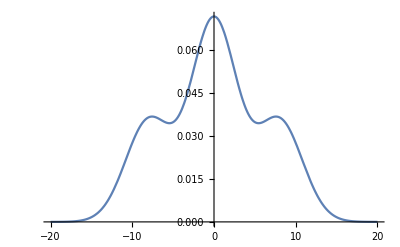

TransformedDistribution[Max[x1,x2],{x1\[Distributed]MixtureDistribution[{1,1},{NormalDistribution[-4,2],NormalDistribution[4,2]}],x2\[Distributed]MixtureDistribution[{1,1},{NormalDistribution[-4,2],NormalDistribution[4,2]}]}]

(ⅇ^(-1/8 (4+x)^2) (1+ⅇ^(2 x)) (Erfc[-(-4+x)/(2 √2)]+Erfc[-(4+x)/(2 √2)]))/(8 √(2 π))

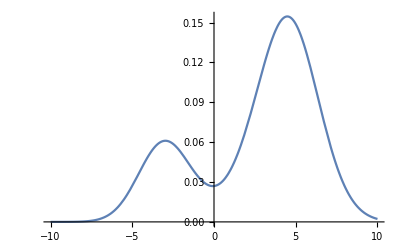

```mathematica
A=NormalDistribution[-4,2]
B=NormalDistribution[4,2]
GMM=MixtureDistribution[{1,1},{A,B}]
f=PDF[GMM,x]
k=2
T1=TransformedDistribution[Sum[Subscript[x, i],{i,1,k}],Table[Subscript[x, i]\[Distributed] GMM,{i,1,k}]]
f2=PDF[T1,x]
Plot[%,{x,-20,20}]
T2=TransformedDistribution[Max[x,y],{x\[Distributed]GMM, y\[Distributed]GMM}]
f3=PDF[T2,x]
Plot[%,{x,-10,10}]
```

```mathematica
FullSimplify[f2]
```

(ⅇ^(-4-x^2/16) (ⅇ^4+Cosh[x]))/(8 √π)

```mathematica
FullSimplify[f3]
```

(ⅇ^(-1/8 (4+x)^2) (1+ⅇ^(2 x)) (2+Erf[(-4+x)/(2 √2)]+Erf[(4+x)/(2 √2)]))/(8 √(2 π))